```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`KdV`;
```

## Normal Reflection Coefficient

General::unfl: Underflow occurred in computation.

{0.+0.680859 ⅈ}

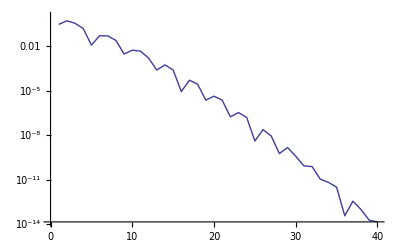
{2.78343×10^-16,-Graphics-}

```mathematica
q[x_]:=1.2Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Defocusing[];
LocatePolesKdV[q,80]
H=ScatteringMatrixFiniteKdV[q,40,6];
H[_?InfinityQ]:={{1,0},{0,1}};
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[2,2]];
bb[k_]:=bb[k]=H[k][[1,2]];
```

```mathematica
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
ρ[0.]:=-1;
h[k_]:=(k^2+1)Sech[k]^2//Abs//N;
SetParams[.4,.1,10.^(-9),20,80];
Setrsamp[h];
SetScatteringData[aa,bb,ρ,LocatePolesKdV[q,80],q]
Settimeflag[False];
startift[];
```

General::unfl: Underflow occurred in computation.

## Cauchy Integral Reflection Coefficient (much faster)

```mathematica
q[x_]:=1.2Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
H=ScatteringMatrixFiniteKdV[q,40,6];
H[_?InfinityQ]={{1,0},{0,1}};
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[2,2]];
bb[k_]:=bb[k]=H[k][[1,2]];
```

{2.78343×10^-16,-Graphics-}

```mathematica
ρ[k_]:=bb[k]/aa[k];
ρ[0.]:=-1;
h[k_]:=(k^2+1)Sech[k]^2//Abs//N;
SetParams[.3,.1,10.^(-9),10,20];
ν=Getnu[];
Setrsamp[h];
up=I(ν+.0001);m=50;el=8;
f={Fun[ρ,Line[{-el,0}-up],m],Fun[ρ,Line[{0,el}-up],m],Fun[ρ,Line[{el,0}+up],2m],Fun[ρ,Line[{0,-el}+up],2m]};
mρ//Clear;
mρ[k_]:=mρ[k]=Piecewise[{{Cauchy[f,k], Im[k]< Im[up]}, {ρ[k], True}}];
SetScatteringData[aa,bb,mρ,LocatePolesKdV[q,80],q]
Settimeflag[False];
startift[];
```

General::unfl: Underflow occurred in computation.

## Setup solution

```mathematica
qKdV//Clear;
qKdV[x_,t_]:=qKdV[x,t]=KdVAuto[x,t];
```

## Plotting: timestring outputs relevant computation times and region information

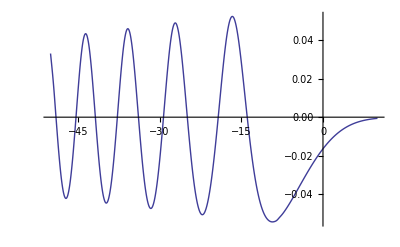

```mathematica
Monitor[TablePlot[qKdV[x,20.]//Re,{x,-50,10,.5},PlotRange->All,InterpolationOrder->2],timestring]
```

Show::shx: No graphical objects to show.

General::stop: Further output of Show :: shx will be suppressed during this calculation.

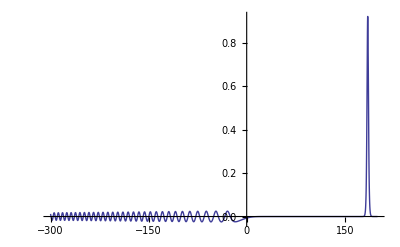

```mathematica
Monitor[TablePlot[qKdV[x,100.]//Re,{x,-300,200,1.},PlotRange->All,InterpolationOrder->2],timestring]
```